```mathematica
(* TECHNOLOGY PARAMETER FITTING *)

(* Clear everything *)
ClearAll["Global`*"]

(* Parameters: modify for each technology *)
maxfact=1.2
techAParams={ρ->0.3*10^-6,Lmax->4*10^-9,wmax->50*10^-9,LT->1*10^-9,w0->0.5*10^-9,Rpar->2000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->240*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techBParams={ρ->0.3*10^-6,Lmax->3*10^-9,wmax->50*10^-9,LT->0.5*10^-9,w0->0.5*10^-9,Rpar->5000,VT->0.4,I0->5*10^14,Ea1->1.2,Ea2->1.2,kT->0.026,gmax->128*10^-6,γ->10^6,w1->1*10^-10,w2->1*10^-9};
techCParams={ρ->8*10^-6,LT->0.4*10^-9,Rpar->10000,VT->0.4,I0->5*10^12,Ea1->1.2,Ea2->1.6,γ->10^9,d1->0.5*10^-9,d2->5*10^-9, ρL->0.25*10^-18,ρA->0.5*10^-9, tau0->1,Lmax->8*10^-9,w0->0.5*10^-9,gmax->40*10^-6,fs->10^6,kT->0.026};
subs=techCParams;

(* Functions for conductance as a function of length and area in Stages 1 and 2 *)
g[A_,L_]:=(VT/(I0 A ⅇ^(-(Lmax-L)/LT))+(ρ L)/A+Rpar)^-1
gs1[L_]:=g[A0,L]
gs2[A_]:=g[A,Lmax]

(* Derivatives of g for Stages 1 and 2 *)
stage1derivative==FullSimplify[gs1'[L]]
stage2derivative==FullSimplify[gs2'[A]]

(* Maximum conductance, length, area *)
gs2inv=FullSimplify[InverseFunction[gs2]];
gs2invfn==FullSimplify[gs2inv[g]]
gs2invderivative==FullSimplify[gs2inv'[g]]
Amax=gs2inv[gmax];
Amaxfn==Amax
A0=(π w0^2)/4;
gtr=g[A0,Lmax];
gtrexpr==gtr
gmax=gmax/.subs;
Amax=InverseFunction[gs2][gmax]*maxfact/.subs;
gtrval==gtr*10^6 Quantity[, "Microsiemens"]/.subs

(* Show components of gtr resistance *)
hopRgtr==(4 VT)/(I0 π w0^2)Quantity[, "Ohms"]/.subs
ohmicRgt==(4 Lmax ρ)/(π w0^2)Quantity[, "Ohms"]/.subs
Rparval==Rpar Quantity[, "Ohms"]/.subs
```

1.2

stage1derivative==-(-ⅇ^((-L+Lmax)/LT) VT+I0 LT ρ)/(A0 I0 LT (Rpar+((ⅇ^((-L+Lmax)/LT) VT)/I0+L ρ)/A0)^2)

stage2derivative==(I0 (VT+I0 Lmax ρ))/(A I0 Rpar+VT+I0 Lmax ρ)^2

gs2invfn==(g (VT+I0 Lmax ρ))/(I0-g I0 Rpar)

gs2invderivative==(VT+I0 Lmax ρ)/(I0 (-1+g Rpar)^2)

Amaxfn==-(gmax (VT+I0 Lmax ρ))/(I0 (-1+gmax Rpar))

gtrexpr==1/(Rpar+(4 VT)/(I0 π w0^2)+(4 Lmax ρ)/(π w0^2))

gtrval==1.3452 μS

hopRgtr==407437. Ω

ohmicRgt==325949. Ω

Rparval==10000 Ω

```mathematica
(* LOAD EXPERIMENTAL DATA *)
Data=SemanticImport[FileNameJoin[{NotebookDirectory[],"data","techC","model.tsv"}]]
times={0.,0.1,1.0,100000.};
ranges={8,16,24,31};
```

Dataset[<>]

```mathematica
(* Get KDEs *)
kdes=Data[GroupBy["range"],GroupBy["timept"],Function[TruncatedDistribution[{0,maxfact gmax},SmoothKernelDistribution[#,MaxMixtureKernels->All]]],"g"];
(*kdes=Data[GroupBy["range"],GroupBy["timept"],Function[TruncatedDistribution[{0,Infinity},EstimatedDistribution[#,NormalDistribution[μ,σ]]]],"g"]*)
kdePDFs=Map[Map[Function[PDF[#,g]]],kdes]
```

Dataset[<>]

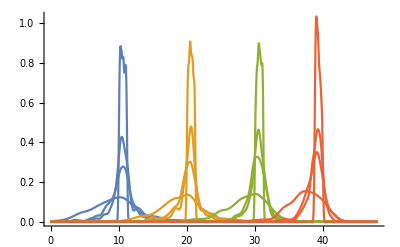

```mathematica
(* Plot some PDFs *)
pdfs=Normal[kdePDFs[KeyTake[ranges],KeyTake[times]][Values,Values]]/10^6/.{g->(x/10^6)};
Plot[pdfs,{x,0,gmax*maxfact*10^6},PlotRange->All]
```

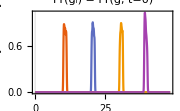

```mathematica
(* Prepare initial conductance distributions and PDFs *)
gidists=Flatten@Normal[kdes[KeyTake[ranges],KeyTake[0.]][Values,Values]];
gidistpdfs=Normal[kdePDFs[KeyTake[ranges],KeyTake[0.]][Values,Values]];
scaled=gidistpdfs/10^6/.{g->(x/10^6)};
Plot[scaled,{x,0,gmax*maxfact*10^6},PlotRange->All,PlotLabel->"Pr(g_i) = Pr(g, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```

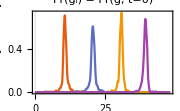

```mathematica
gfexactdists=Flatten@Normal[kdes[KeyTake[ranges],KeyTake[0.01]][Values,Values]];
gfexactdistpdfs=Normal[kdePDFs[KeyTake[ranges],KeyTake[0.01]][Values,Values]];
scaled=gfexactdistpdfs/10^6/.{g->(x/10^6)};
Plot[scaled,{x,0,gmax*maxfact*10^6},PlotRange->All,PlotLabel->"Pr(g_i) = Pr(g, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```

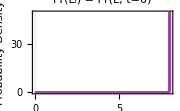

LidistVar=={6.4×10^-23,6.4×10^-23,6.4×10^-23,6.4×10^-23}

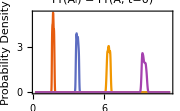

AidistVar=={4.37555×10^-39,7.39001×10^-39,1.19415×10^-38,2.05661×10^-38}

```mathematica
(* TRANSLATE CONDUCTANCE DISTRIBUTIONS TO AREA/LENGTH DISTRIBUTIONS *)

(* Use interpolation for inverse function, then sample and generate KDE *)
npts=1000;
nsamps=1000;

Off[General::munfl]
LDist[samps_]:=If[Variance[samps]>0,KernelMixtureDistribution[samps,MaxMixtureKernels->All],NormalDistribution[Mean[samps]-5*Lmax/npts,Lmax/npts]]/.subs
ADist[samps_]:=If[Variance[samps]>0,KernelMixtureDistribution[samps,MaxMixtureKernels->All],NormalDistribution[Mean[samps]+5*(Amax-A0)/npts,(Amax-A0)/npts]]/.subs

(* Length as function of conductance *)
gs1invpts=Table[{gs1[L]/.subs,L},{L,0,Lmax,Lmax/npts}]/.subs;
PrependTo[gs1invpts,{0,0}];
AppendTo[gs1invpts,{1.2*gmax,Lmax}]/.subs;
gs1inv=Interpolation[gs1invpts,InterpolationOrder->1]; 

(* Area as function of conductance *)
gs2invpts=Table[{gs2[A]/.subs,A},{A,A0,Amax,(Amax-A0)/npts}];
PrependTo[gs2invpts,{0,A0}];
gs2inv=Interpolation[gs2invpts,InterpolationOrder->1]; 

(* Length distribution *)
Lidists=Table[TransformedDistribution[gs1inv[g],g\[Distributed]gidist],{gidist,gidists}];
Lisamps=Table[RandomVariate[Lidist,nsamps],{Lidist,Lidists}];
LidistKDEs=Table[LDist[Lisamp],{Lisamp,Lisamps}];
LidistKDEpdfs=Table[PDF[LidistKDE,L],{LidistKDE,LidistKDEs}];
scaled=LidistKDEpdfs/10^9/.{L->x/10^9};
Plot[scaled,{x,0,Lmax*10^9}/.subs,PlotRange->All,PlotLabel->"Pr(L_i) = Pr(L, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Length (nm)",None}}]
LidistVar==N@Map[Variance,LidistKDEs]

(* Area distribution *)
Aidists=Table[TransformedDistribution[gs2inv[g],g\[Distributed]gidist],{gidist,gidists}];
Aisamps=Table[RandomVariate[Aidist,nsamps],{Aidist,Aidists}];
AidistKDEs=Table[ADist[Aisamp],{Aisamp,Aisamps}];
AidistKDEpdfs=Table[PDF[AidistKDE,A],{AidistKDE,AidistKDEs}];
scaled=AidistKDEpdfs/10^18/.{A->x/10^18};
Plot[scaled,{x,A0*10^18,Amax*10^18}/.subs,PlotRange->All,PlotLabel->"Pr(A_i) = Pr(A, t=0)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Initial Area (nm^2)",None}}]
AidistVar==Map[Variance,AidistKDEs]

(* 3D plot *)
(*Pjoint=(LidistKDEpdfs/10^9/.{L->x/10^9})(AidistKDEpdfs/10^18/.{A->y/10^18});
Plot3D[Pjoint,{x,0,(Lmax-5*Lmax/npts)*10^9/.subs},{y,(A0+5*(Amax-A0)/npts)*10^18,Amax*10^18}/.subs,PlotRange->All,PlotLabel->"Pr(A_i, L_i) = Pr(A, L, t=0)",Exclusions->None,PlotPoints->100,PlotTheme->"Scientific",AxesLabel->{"Length (nm)", "Area (nm^2)", "Prob. Density"},BoxRatios->{1, 1, 1}]*)
```

(π w0^6 ρL^2 Log[0.01 fs])/((-Ea1+Ea2)/kT+(-d1+d2) γ)

-(157.08 kT w0^6 ρL^2 (-4.60517+Log[fs]))/(Ea1-1. Ea2+(d1-1. d2) kT γ)

7.10523×10^-92

3/1000000000000000000000

(π w0^6 ρA^2 Log[0.01 fs])/((-Ea1+Ea2)/kT+(-d1+d2) γ)

-(157.08 kT w0^6 ρA^2 (-4.60517+Log[fs]))/(Ea1-1. Ea2+(d1-1. d2) kT γ)

2.84209×10^-73

1/500000000000000000000000000000000000

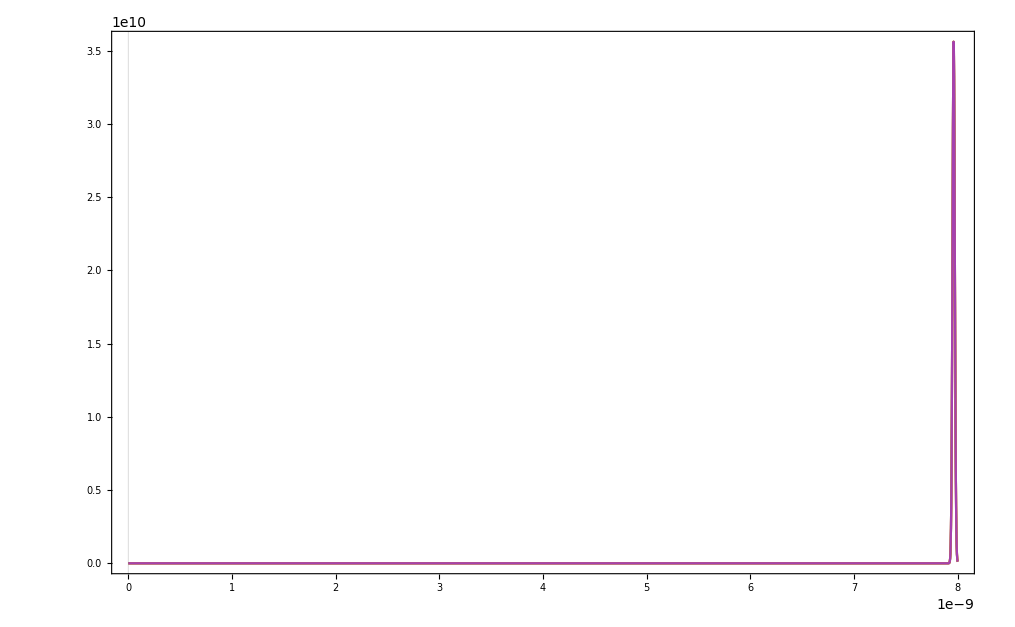

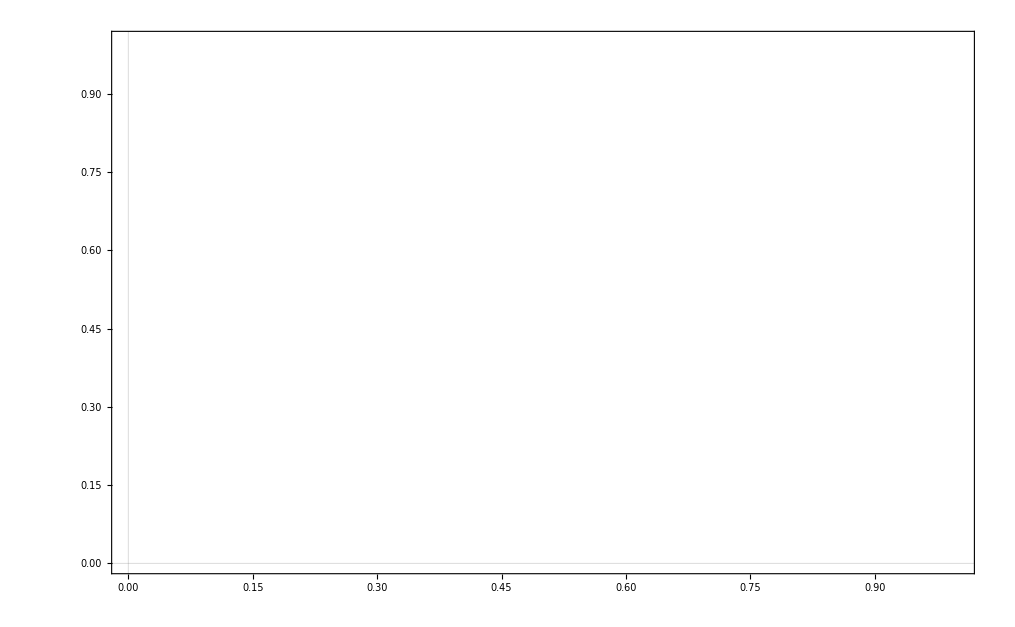

```mathematica
(* SOLVE FOR FINAL LENGTH/AREA DISTRIBUTIONS *)

(* Mesh points setting *)
meshpts=2000;

(* Final time to solve for *)
tf=0.01;

(* Compute constants *)
varL=( ρL w0^3 )^2(π Log[fs tf])/((Ea2 - Ea1)/kT + γ(d2-d1))
DiffL=Simplify[PowerExpand[varL/(2tf)]]
N[DiffL/.subs]
DiffL=3*10^-21

varA=( ρA w0^3 )^2(π Log[fs tf])/((Ea2 - Ea1)/kT + γ(d2-d1))
DiffA=Simplify[PowerExpand[varA/(2tf)]]
N[DiffA/.subs]
DiffA=2*10^-36

(* Solve diffusion equation for length with initial/boundary conditions *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->Lmax/meshpts/.subs}}}};
heqn=D[p[L,t],t]-D[DiffL p[L,t],{L,2}]==NeumannValue[0,L==0]+NeumannValue[0,L==Lmax/.subs];
ics=Table[p[L,0]==icfn,{icfn,LidistKDEpdfs}];
Lfpdfs=p[L,tf]/.Table[NDSolve[{heqn/.subs,ic},p[L,tf],{L,0,Lmax}/.subs,{t,0,tf},InterpolationOrder->All,Method->method],{ic,ics}];
Plot[Lfpdfs,{L,0,Lmax}/.subs,PlotRange->All,PlotTheme->"Scientific"]

(* Solve diffusion equation for area with initial/boundary conditions *)
method={"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->(Amax-A0)/meshpts/.subs}}}};
heqn=D[p[A,t],t]-D[DiffA p[A,t],{A,2}]==NeumannValue[0,A==A0]+NeumannValue[0,A==Amax];
ics=Table[p[A,0]==icfn,{icfn,AidistKDEpdfs}];
Afpdfs=p[A,tf]/.Table[NDSolve[{heqn/.subs,ic},p[A,tf],{A,A0,Amax}/.subs,{t,0,tf},InterpolationOrder->All,Method->method],{ic,ics}];
Plot[Afpdfs,{A,A0,Amax}/.subs,PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
Table[NIntegrate[A^2 Abs[Afpdf[[1]]],{A,A0,Amax}/.subs,MaxRecursion->15]-(NIntegrate[A Abs[Afpdf[[1]]],{A,A0,Amax}/.subs,MaxRecursion->15])^2,{Afpdf,Afpdfs}]
varfexactA
Table[NIntegrate[L^2 Abs[Lfpdf[[1]]],{L,0,Lmax}/.subs,MaxRecursion->15]-(NIntegrate[L Abs[Lfpdf[[1]]],{L,0,Lmax}/.subs,MaxRecursion->15])^2,{Lfpdf,Lfpdfs}]
varfexactL
```

{2.41355×10^-38,3.70749×10^-38,5.98353×10^-38,1.00428×10^-37,1.51259×10^-37}

varfexactA

{1.52325×10^-17,3.56579×10^-23,3.56579×10^-23,3.56579×10^-23,3.56579×10^-23}

varfexactL

```mathematica
(* TRANSLATE LENGTH/AREA DISTRIBUTIONS BACK TO CONDUCTANCE DISTRIBUTIONS *)
npts=1000;
Table[NIntegrate[Abs[Afpdf[[1]]],{A,A0,Amax}/.subs,MaxRecursion->15],{Afpdf,Afpdfs}]
Table[NIntegrate[Abs[Lfpdf[[1]]],{L,0,Lmax}/.subs,MaxRecursion->15],{Lfpdf,Lfpdfs}]
wfdists=ParallelTable[Normal@ProbabilityDistribution[Abs[Afpdf[[1]]],{A,A0,Amax}/.subs,Method->"Normalize"],{Afpdf,Afpdfs}]
Lfdists=ParallelTable[Normal@ProbabilityDistribution[Abs[Lfpdf[[1]]],{L,0,Lmax}/.subs,Method->"Normalize"],{Lfpdf,Lfpdfs}]
(*gfdists=MapThread[TransformedDistribution[g[A,L],{A\[Distributed]#1,L\[Distributed]#2}]&,{wfdists,Lfdists}]*)
gfdists=ParallelMap[TransformedDistribution[g[A,L],{A\[Distributed]#1,L\[Distributed]#2}]&@@#&,{wfdists,Lfdists}//Transpose]
```

{1.,1.,1.,1.}

{1.,1.,1.,1.}

{ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}]}

{ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}],ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}],ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}],ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}]}

{TransformedDistribution[1/(Rpar+(ⅇ^((-L+Lmax)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((-L+Lmax)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((-L+Lmax)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}]}],TransformedDistribution[1/(Rpar+(ⅇ^((-L+Lmax)/LT) VT)/(A I0)+(L ρ)/A),{A\[Distributed]ProbabilityDistribution[1. Abs[                                 -19          -17
InterpolatingFunction[{{1.9635 10   , 1.152 10   }, {0., 0.01}}, <>][x,0.01]],{x,1.9635×10^-19,1.152×10^-17}],L\[Distributed]ProbabilityDistribution[1. Abs[                                 -9
InterpolatingFunction[{{0., 8. 10  }, {0., 0.01}}, <>][x,0.01]],{x,0,1/125000000}]}]}

```mathematica
(* SAMPLE FINAL CONDUCTANCE DISTRIBUTIONS AND CREATE PDF *)
nsamps=1000;
gfsamps=ParallelTable[RandomVariate[gfdist/.subs,nsamps],{gfdist,gfdists}] ;
gfdistKDEs=ParallelTable[SmoothKernelDistribution[gfsamp,MaxMixtureKernels->All],{gfsamp,gfsamps}];
gfdistKDEpdfs=ParallelTable[PDF[gfdistKDE,g],{gfdistKDE,gfdistKDEs}];
(*data=Transpose[{gfdistKDEpdfs,gidistpdfs}];*)
```

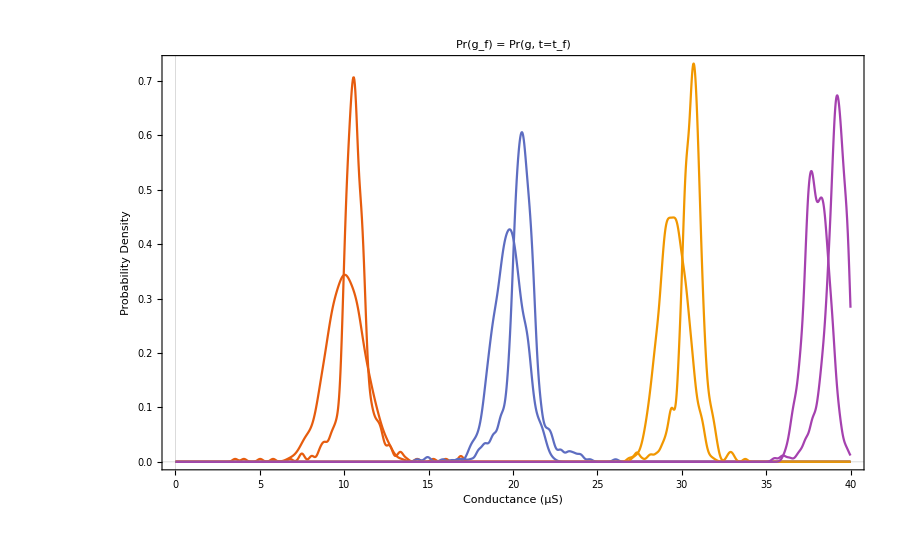

```mathematica
(* PLOT FINAL CONDUCTANCE DISTRIBUTIONS *)

(* Final conductance distributions *)
scaled=Transpose[{gfdistKDEpdfs,gfexactdistpdfs}]/10^6/.{g->x/10^6};
(*scaled=gfdistKDEpdfs/10^6/.{g->x/10^6};*)
Plot[scaled,{x,0,gmax*10^6},PlotRange->All,PlotLabel->"Pr(g_f) = Pr(g, t=t_f)",Exclusions->None,PlotTheme->"Scientific",PlotPoints->1000,ImageSize->Small,Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]

(* Plot final joint area/length probability distribution *)

(* 3D plot *)
(*Pjoint=(Lfpdfs/10^9/.{L->x/10^9})(Afpdfs/10^18/.{A->y/10^18});
Plot3D[Pjoint,{x,0,Lmax*10^9},{y,A0*10^18,Amax*10^18},PlotRange->All,PlotLabel->"Pr(A_f, L_f) = Pr(A, L, t=t_f)",Exclusions->None,PlotPoints->100,PlotTheme->"Scientific"]*)
```

```mathematica
Map[Variance,gfdistKDEs]
Map[Variance,gfexactdists]
```

{1.37264×10^-12,9.17482×10^-13,7.07637×10^-13,5.31936×10^-13}

{1.2649×10^-12,1.20966×10^-12,6.03656×10^-13,6.1597×10^-13}